```mathematica
Exit[];
```

```mathematica
hedge=Flatten[Import["c:\\book1.txt","Table"],1][[1;;120]];
```

```mathematica
Length[hedge]
```

120

```mathematica
g=FinancialData["DAX","1.1.2004"];
```

```mathematica
d2=Transpose[g][[2]][[1;;Length[hedge]]];
```

```mathematica
dax=Transpose[g][[2]][[1;;Length[hedge]]];
```

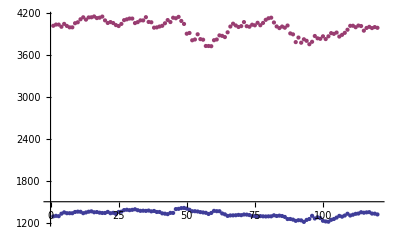

```mathematica
ListPlot[{hedge,dax}]
```

```mathematica
Export["c:\\outt.csv",Transpose[{hedge,dax,d2}]]
```

c:\outt.csv

```mathematica
hedge=Log[hedge];dax=Log[dax];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];
```

```mathematica
w=Transpose[{hedge,co}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
d2=Transpose[w][[3]];
```

Part::partw: Part 3 of {{-0.0312825, -0.0298387, -0.0237205, -0.0236975, -0.0193645, -0.0178444, -0.0169541, -0.0152089, -0.0149422, -0.0148138, « 109 »}, {« 1 »}} does not exist.

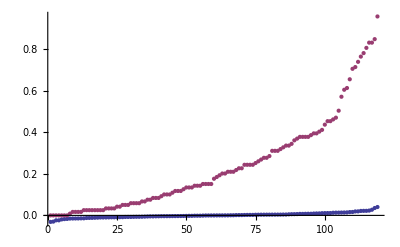

```mathematica
ListPlot[Transpose[w][[1;;2]],PlotRange->All]
```

```mathematica
min0=Min[Transpose[w][[1]]];wN=Length[hedge];nn=wN;
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤nn,i++,
AppendTo[U,{hedge[[i]],max1,(i-1)/nn}];
AppendTo[U,{max0,sdax[[i]],(i-1)/nn}];
AppendTo[U,{hedge[[i]],min1,0}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<w[[i,1]]  && #[[2]]<w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
hedgeI=Table[{hedge[[i]],(i-1)/(nn-1)},{i,nn}];
daxI=Table[{sdax[[i]],(i-1)/(nn-1)},{i,nn}];W=F;Co=Table[{Select[hedgeI,#[[1]]==W[[i,1]]&][[1,2]],Select[daxI,#[[1]]==W[[i,2]]&][[1,2]],W[[i,3]]},{i,Length[W]}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
ListPointPlot3D[Co]
```

-Graphics3D-

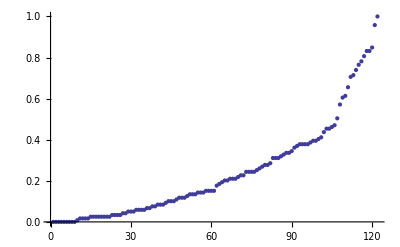

```mathematica
ListPlot[Sort[Transpose[Co][[3]]]]
```

```mathematica
co=Sort[Transpose[W][[3]]];
```

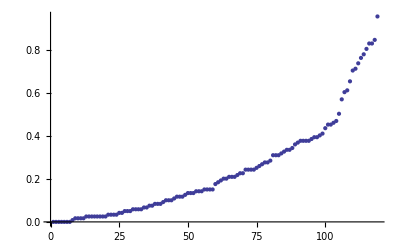

```mathematica
ListPlot[Sort[Transpose[W][[3]]]]
```

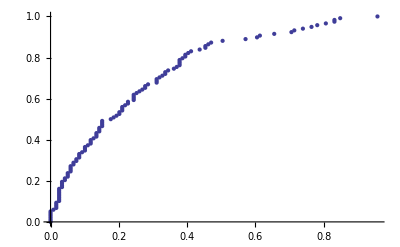

```mathematica
ListPlot[coI]
```

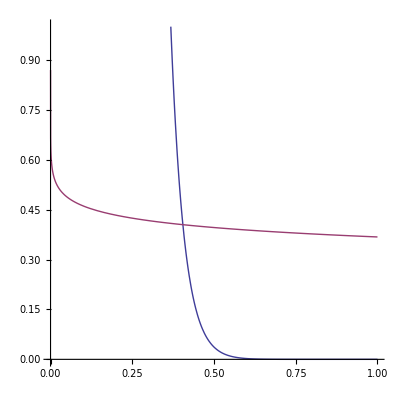

```mathematica
o=9;Plot[{(-Log[x])^o,Exp[-x^(1/o)]},{x,0,1},AspectRatio->1,PlotRange->{0,1}]
```

```mathematica
Co2=Table[{Select[hedgeI,#[[1]]==W[[i,1]]&][[1,2]],Select[coI,#[[1]]==W[[i,2]]&][[1,2]],W[[i,3]]},{i,Length[W]}];AppendTo[Co,{1,0,0}];
```

{{0,6/59,0},{1/118,3/118,0},{1/59,42/59,2/119},{3/118,21/118,2/119},{2/59,69/118,3/119},{5/118,43/59,5/119},{3/59,52/59,6/119},{7/118,44/59,6/119},{4/59,75/118,4/119},{9/118,91/118,8/119},{5/59,1/2,3/119},{11/118,23/59,3/119},{6/59,29/59,4/119},{13/118,85/118,9/119},{7/59,109/118,2/17},{15/118,95/118,13/119},{8/59,9/59,2/119},{17/118,13/59,4/119},{9/59,5/59,1/119},{19/118,35/59,10/119},{10/59,54/59,19/119},{21/118,45/59,16/119},{11/59,40/59,12/119},{23/118,117/118,23/119},{12/59,71/118,11/119},{25/118,4/59,1/119},{13/59,25/118,6/119},{27/118,19/59,8/119},{14/59,37/59,15/119},{29/118,43/118,9/119},{15/59,65/118,13/119},{31/118,45/118,10/119},{16/59,53/118,12/119},{33/118,16/59,8/119},{17/59,36/59,20/119},{35/118,17/59,9/119},{18/59,41/59,25/119},{37/118,97/118,33/119},{19/59,10/59,5/119},{39/118,77/118,25/119},{20/59,27/59,16/119},{41/118,14/59,9/119},{21/59,56/59,41/119},{43/118,8/59,4/119},{22/59,51/118,1/7},{45/118,103/118,40/119},{23/59,34/59,23/119},{47/118,27/118,10/119},{24/59,1/59,0},{49/118,81/118,2/7},{25/59,33/118,2/17},{51/118,21/59,1/7},{26/59,115/118,3/7},{53/118,51/59,46/119},{27/59,57/118,24/119},{55/118,67/118,4/17},{28/59,111/118,53/119},{57/118,53/59,3/7},{29/59,2/59,2/119},{1/2,32/59,4/17},{30/59,22/59,20/119},{61/118,47/118,23/119},{31/59,37/118,1/7},{63/118,83/118,45/119},{32/59,26/59,26/119},{65/118,24/59,25/119},{33/59,55/59,62/119},{67/118,57/59,65/119},{34/59,105/118,59/119},{69/118,11/118,5/119},{35/59,1,10/17},{71/118,38/59,44/119},{36/59,5/118,3/119},{73/118,29/118,16/119},{37/59,23/118,12/119},{75/118,58/59,73/119},{38/59,46/59,59/119},{77/118,39/59,7/17},{39/59,25/59,30/119},{79/118,28/59,5/17},{40/59,48/59,64/119},{81/118,31/118,18/119},{41/59,89/118,61/119},{83/118,17/118,9/119},{42/59,107/118,74/119},{85/118,11/59,13/119},{43/59,63/118,6/17},{87/118,7/59,8/119},{44/59,33/59,46/119},{89/118,49/59,73/119},{45/59,87/118,65/119},{91/118,73/118,53/119},{46/59,31/59,43/119},{93/118,61/118,43/119},{47/59,15/118,9/119},{95/118,101/118,79/119},{48/59,15/59,22/119},{97/118,18/59,27/119},{49/59,49/118,37/119},{99/118,1/118,0},{50/59,99/118,83/119},{101/118,93/118,79/119},{51/59,12/59,18/119},{103/118,13/118,9/119},{52/59,3/59,5/119},{105/118,39/118,2/7},{53/59,0,0},{107/118,79/118,71/119},{54/59,35/118,32/119},{109/118,47/59,87/119},{55/59,30/59,54/119},{111/118,50/59,94/119},{56/59,55/118,50/119},{113/118,20/59,37/119},{57/59,19/118,1/7},{115/118,9/118,8/119},{58/59,113/118,111/119},{117/118,7/118,1/17},{1,41/118,41/119},{1,0,0},{0,1,0},{1,1,1}}

```mathematica
Show[ListPlot3D[Co,Mesh->All],ListPointPlot3D[Co,PlotStyle->Red]]
```

-Graphics3D-